# Expanding BEC

Y. Castin and R. Dum (https://doi.org/10.1103/PhysRevLett.77.5315) have shown that a pure BEC expanding from a harmonic trap that is turned off at t=0 can be well approximated as a rescaling of the x,y,z coordinates of the original solution 

 N(|Φ(r⃗,t)|)_TF^2=(μ- ∑_(j=1)^3 1/2 m ω_j^2(0) (r_j/(λ_j(t)))^2)/(gλ_1(t)λ_2(t)λ_3(t))

```mathematica
DSolve[{λx''[t]==(ωx)^2/((λx[t]^2)λy [t]λz[t]),λx'[0]==0,λx[0]==1,
λy''[t]==(ωy)^2/(λx[t](λy[t])^2 λz[t]),λy'[0]==0,λy[0]==1,
λz''[t]==(ωz)^2/(λx[t]λy[t] (λz[t])^2),λz'[0]==0,λz[0]==1},
{λx[t],λy[t],λz[t]},t]
```

DSolve[{λx''[t]==ωx^2/(λx[t]^2 λy[t] λz[t]),λx'[0]==0,λx[0]==1,λy''[t]==ωy^2/(λx[t] λy[t]^2 λz[t]),λy'[0]==0,λy[0]==1,λz''[t]==ωz^2/(λx[t] λy[t] λz[t]^2),λz'[0]==0,λz[0]==1},{λx[t],λy[t],λz[t]},t]

{{λx[t]→InterpolatingFunction[…][t],λy[t]→InterpolatingFunction[…][t],λz[t]→InterpolatingFunction[…][t]}}

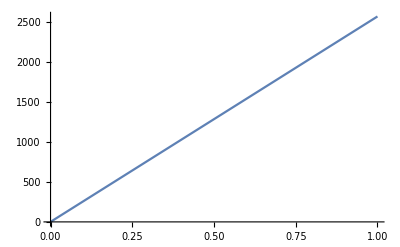

```mathematica
omegasamp={500,500,500}*2π;
numericscaling=NDSolve[{λx''[t]==omegasamp[[1]]^2/((λx[t]^2)λy [t]λz[t]),λx'[0]==0,λx[0]==1,
λy''[t]==omegasamp[[1]]^2/(λx[t](λy[t])^2 λz[t]),λy'[0]==0,λy[0]==1,
λz''[t]==omegasamp[[1]]^2/(λx[t]λy[t] (λz[t])^2),λz'[0]==0,λz[0]==1},
{λx[t],λy[t],λz[t]},{t,0,1}]
Plot[Evaluate[λx[t]/.numericscaling[[1]]],{t,0,1}]
```

{λx→ParametricFunction[<>],λy→ParametricFunction[<>],λz→ParametricFunction[<>]}

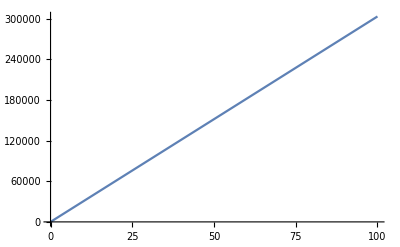

```mathematica
parametricScaling=ParametricNDSolve[{λx''[t]==(ωx)^2/((λx[t]^2)λy [t]λz[t]),λx'[0]==0,λx[0]==1,
λy''[t]==(ωy)^2/(λx[t](λy[t])^2 λz[t]),λy'[0]==0,λy[0]==1,
λz''[t]==(ωz)^2/(λx[t]λy[t] (λz[t])^2),λz'[0]==0,λz[0]==1},
{λx,λy,λz},{t,0,10},{ωx,ωy,ωz},AccuracyGoal->10,PrecisionGoal->10]
Plot[λx[Sequence@@omegasamp][t]/.parametricScaling,{t,0,100}]
```

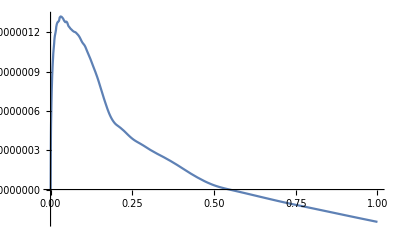

```mathematica
Plot[{(λx[Sequence@@omegasamp][t]/.parametricScaling)-(Evaluate[λx[t]/.numericscaling[[1]]])},{t,0,1}]
```

### Approx solution

in the paper there is an approx solution for the cyl. symetric case
ωx=ωy=ωtight
ωz=ωweak

```mathematica
ReturnFracErr:=Function[{tvals,omegasamp,parametricNumSoln,analyticalSoln},
	{
	((λx[Sequence@@omegasamp][tvals]/.parametricNumSoln)-(λx/.analyticalSoln))/(λx[Sequence@@omegasamp][tvals]/.parametricNumSoln),
	((λy[Sequence@@omegasamp][tvals]/.parametricNumSoln)-(λy/.analyticalSoln))/(λx[Sequence@@omegasamp][tvals]/.parametricNumSoln),
	((λz[Sequence@@omegasamp][tvals]/.parametricNumSoln  )-(λz/.analyticalSoln))/(λz[Sequence@@omegasamp][tvals]/.parametricScaling  )
	}/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]],t->tvals}
]
```

```mathematica
makeComparisonPlots:=Function[{trangeplot,omegasamp,parametricNumSoln,analyticalSoln},

	p1=Plot[{
		λx[Sequence@@omegasamp][t]/.parametricNumSoln,
		λy[Sequence@@omegasamp][t]/.parametricNumSoln,
		λx/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]},
		λy/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}
		},
		{t,tmaxplot[[1]],tmaxplot[[2]]},
		ImageSize->Small,
		Frame->True,
		ImageMargins->0,
		FrameLabel->{{"rescaling value x,y",None},{"time",None}}
		];
	p2=Plot[{
		(λz[Sequence@@omegasamp][t]/.parametricNumSoln  ),
		(λz/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})
		},
		{t,tmaxplot[[1]],tmaxplot[[2]]},
		Frame->True,
		ImageSize->Small,
		FrameLabel->{{"rescaling value z",None},{"time",None}}
		];
	p3=Plot[{
		(λx[Sequence@@omegasamp][t]/.parametricNumSoln)-(λx/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}),
		(λy[Sequence@@omegasamp][t]/.parametricNumSoln)-(λy/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})
		},
		{t,tmaxplot[[1]],tmaxplot[[2]]},
		ImageSize->Small,
		Frame->True,
		ImageMargins->0,
		FrameLabel->{{"error x,y",None},{"time",None}}
		];
	p4=Plot[{
			((λz[Sequence@@omegasamp][t]/.parametricNumSoln  )-
		(λz/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}))/(λz[Sequence@@omegasamp][t]/.parametricScaling  )
		},
		{t,tmaxplot[[1]],tmaxplot[[2]]},
		AxesLabel->{"time","error z"},
		Frame->True,
		ImageSize->Small];
	p5=Plot[{
		((λx[Sequence@@omegasamp][t]/.parametricNumSoln)-(λx/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}))/(λx[Sequence@@omegasamp][t]/.parametricNumSoln),
		((λy[Sequence@@omegasamp][t]/.parametricNumSoln)-(λy/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}))/(λx[Sequence@@omegasamp][t]/.parametricNumSoln)
		},
		{t,tmaxplot[[1]],tmaxplot[[2]]},
		ImageSize->Small,
		Frame->True,
		ImageMargins->0,
		FrameLabel->{{"frac error x,y",None},{"time",None}}
		];
	p6=Plot[{
			((λz[Sequence@@omegasamp][t]/.parametricNumSoln  )-(λz/.analyticalSoln/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}))/(λz[Sequence@@omegasamp][t]/.parametricScaling  )
		},
		{t,tmaxplot[[1]],tmaxplot[[2]]},
		FrameLabel->{{"x frac error",None},{"time",None}},
		Frame->True,
		ImageSize->Small];
GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6}},ImageSize->1000,Spacings->0.3]
]
```

```mathematica
approxCigarSoln={λtight->√(1+(ωtight*t)^2),λweak->1+(ωweak/ωtight)^2((ωtight   t) ArcTan[ωtight   t]-Log[√(1+(ωtight*t)^2)])}
```

{λtight→√(1+t^2 ωtight^2),λweak→1+(ωweak^2 (t ωtight ArcTan[t ωtight]-Log[√(1+t^2 ωtight^2)]))/ωtight^2}

900 π

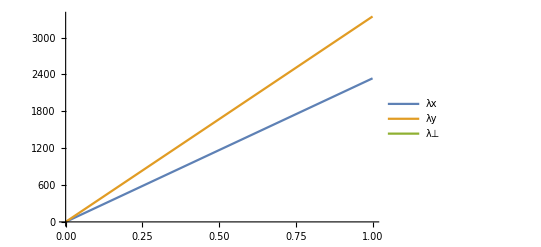

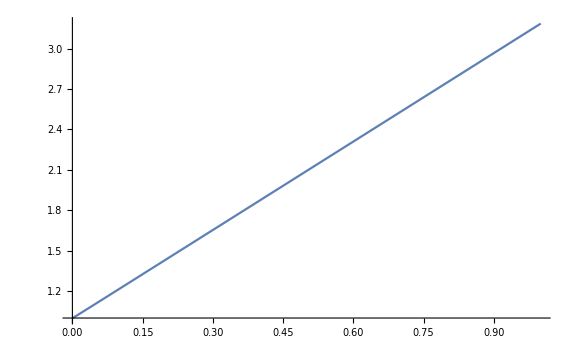

```mathematica
omegasamp={400,500,10}*2π;
omegatightapprox=1/2(omegasamp[[1]]+omegasamp[[2]])
Plot[{λx[Sequence@@omegasamp][t]/.parametricScaling,λy[Sequence@@omegasamp][t]/.parametricScaling,λtight/.approxCigarSoln/.{ωtight->omegatightapprox,ωweak->omegasamp[[3]]}},{t,0,1},PlotLegends->{"λx","λy","λ⊥"}]
Plot[{λz[Sequence@@omegasamp][t]/.parametricScaling,λweak/.approxCigarSoln/.{ωtight->omegatightapprox,ωweak->omegasamp[[3]]}},{t,0,1}]
```

```mathematica
approxCigarSoln={λx->√(1+((ωx+ωy)1/2*t)^2),λy->√(1+((ωx+ωy)1/2*t)^2),λz->1+((2ωz)/(ωx+ωy))^2(((ωx+ωy)1/2   t) ArcTan[(ωx+ωy)1/2  t]-Log[√(1+((ωx+ωy)1/2 t)^2)])}
tmaxplot={0.1,100};
omegasamp={500,400,50}*2π;
makeComparisonPlots[tmaxplot,omegasamp,parametricScaling,approxCigarExtendedSoln]
```

{λx→√(1+1/4 t^2 (ωx+ωy)^2),λy→√(1+1/4 t^2 (ωx+ωy)^2),λz→1+(4 ωz^2 (1/2 t (ωx+ωy) ArcTan[1/2 t (ωx+ωy)]-Log[√(1+1/4 t^2 (ωx+ωy)^2)]))/(ωx+ωy)^2}

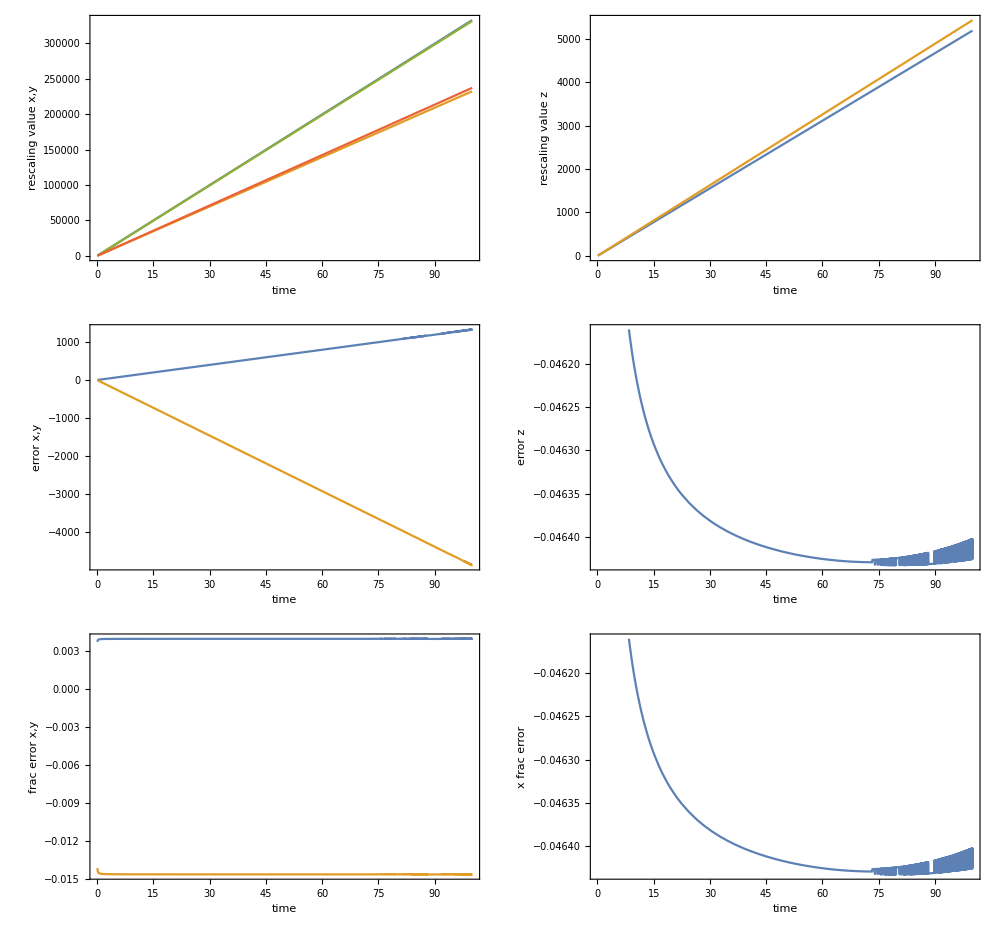

{λx→(2 ωx √(1+1/4 t^2 (ωx+ωy)^2))/(ωx+ωy),λy→(2 ωy √(1+1/4 t^2 (ωx+ωy)^2))/(ωx+ωy),λz→1+(4 ωz^2 (1/2 t (ωx+ωy) ArcTan[1/2 t (ωx+ωy)]-Log[√(1+1/4 t^2 (ωx+ωy)^2)]))/(ωx+ωy)^2}

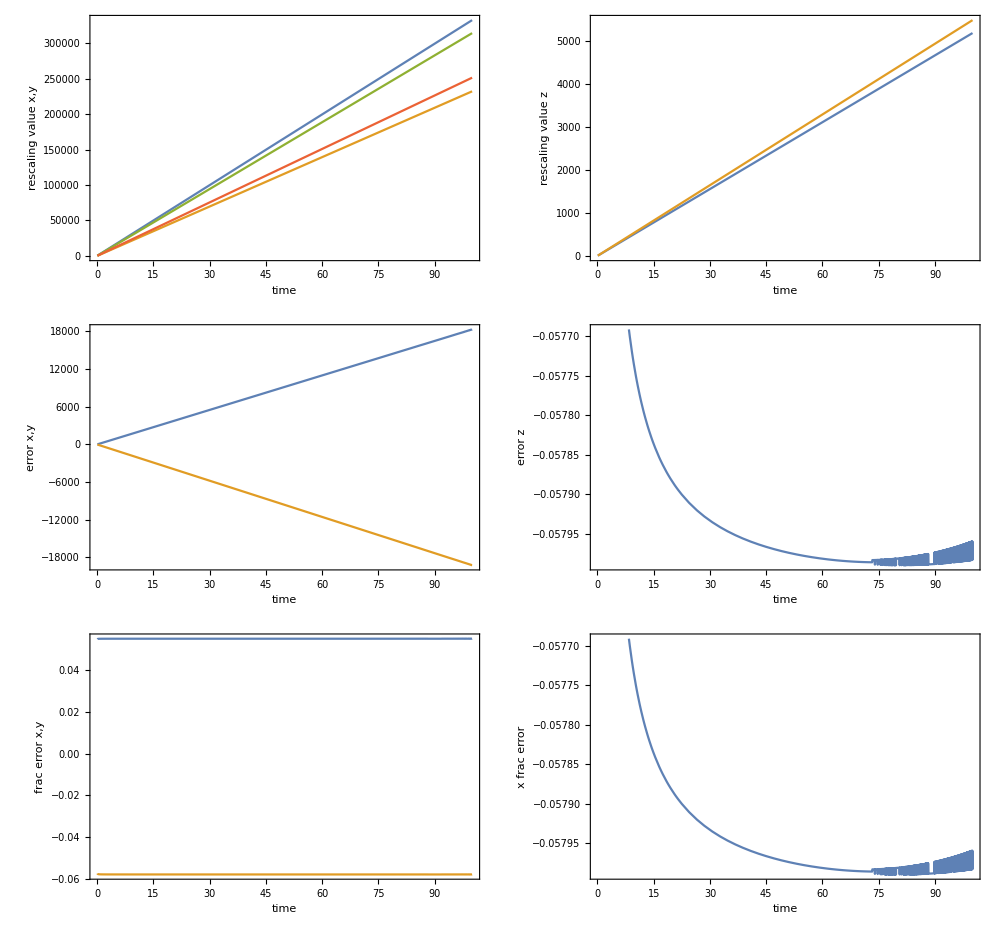

```mathematica
approxCigarExtendedSoln={λx->(2ωx)/(ωx+ωy)√(1+((ωx+ωy)1/2*t)^2),λy->(2ωy)/(ωx+ωy)√(1+((ωx+ωy)1/2*t)^2),λz->1+((2ωz)/(ωx+ωy))^2(((ωx+ωy)1/2   t) ArcTan[(ωx+ωy)1/2  t]-Log[√(1+((ωx+ωy)1/2 t)^2)])}
tmaxplot={0.1,100};
omegasamp={500,400,50}*2π;
makeComparisonPlots[tmaxplot,omegasamp,parametricScaling,approxCigarExtendedSoln]
```

{λx→2 √2 (ωx/(ωx+ωy))^(3/2) √(1+1/4 t^2 (ωx+ωy)^2) (1-(4 ωz)/(19 (ωx+ωy))),λy→2 √2 (ωy/(ωx+ωy))^(3/2) √(1+1/4 t^2 (ωx+ωy)^2) (1-(4 ωz)/(19 (ωx+ωy))),λz→1+(4 ωz^2 (1-ωz/(ωx+ωy)) (1/2 t (ωx+ωy) ArcTan[1/2 t (ωx+ωy)]-Log[√(1+1/4 t^2 (ωx+ωy)^2)]))/(ωx+ωy)^2}

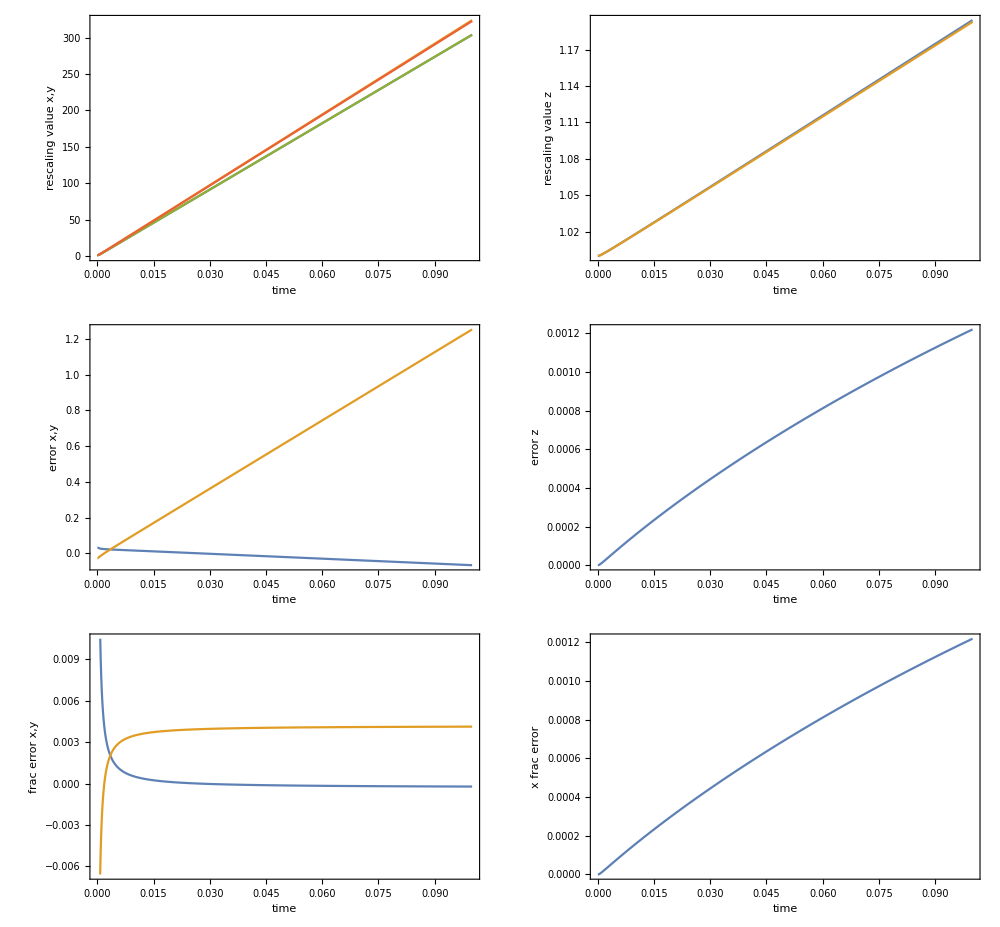

```mathematica
approxCigarHackExtendedSoln={λx->(((2ωx)/(ωx+ωy))^(6/4)(1-4/38((2ωz)/(ωx+ωy))))√(1+((ωx+ωy)1/2*t)^2),λy->(((2ωy)/(ωx+ωy))^(6/4)(1-4/38((2ωz)/(ωx+ωy))))√(1+((ωx+ωy)1/2*t)^2),λz->1+(1-1/2((2ωz)/(ωx+ωy)))((2ωz)/(ωx+ωy))^2(((ωx+ωy)1/2   t) ArcTan[(ωx+ωy)1/2  t]-Log[√(1+((ωx+ωy)1/2 t)^2)])}
tmaxplot={0.0,0.1};
omegasamp={490,510,10}*2π;
makeComparisonPlots[tmaxplot,omegasamp,parametricScaling,approxCigarHackExtendedSoln]
```

{λx→1+√2 t ωx √(ωx/(ωx+ωy)) (1-(4 ωz)/(19 (ωx+ωy))),λy→1+√2 t ωy √(ωy/(ωx+ωy)) (1-(4 ωz)/(19 (ωx+ωy))),λz→1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2}

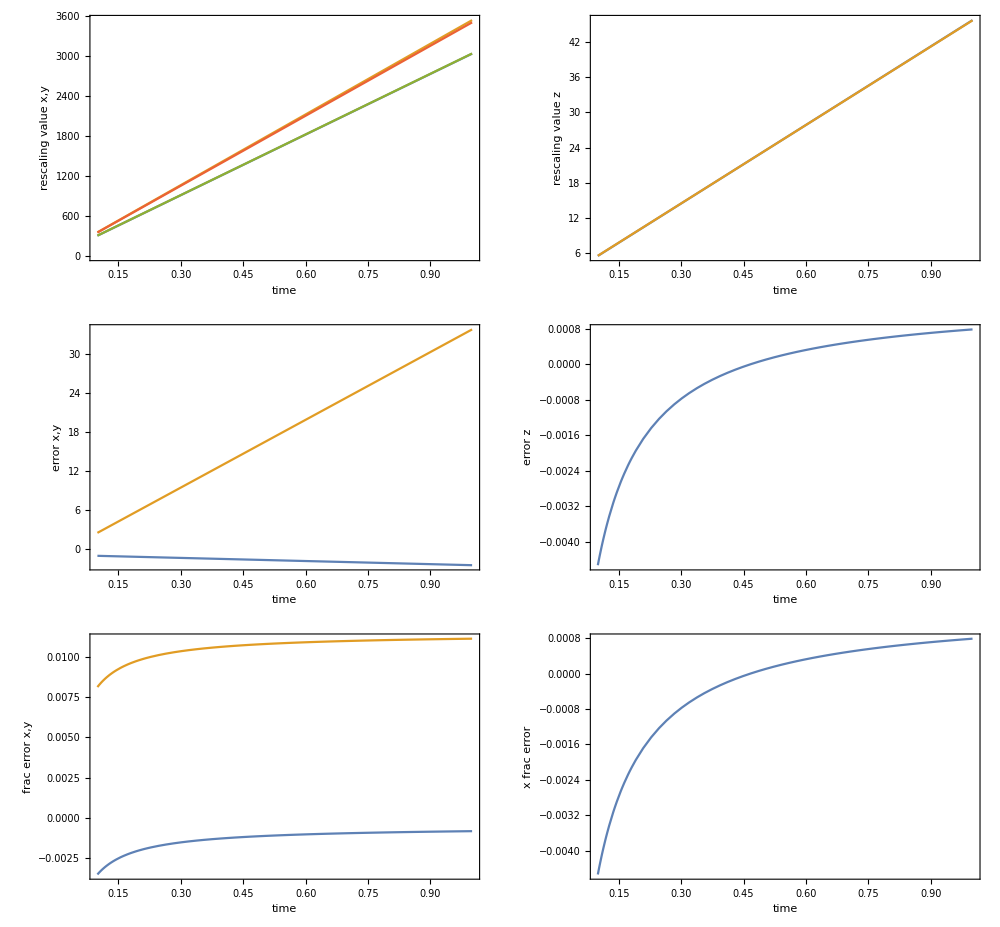

```mathematica
approxCigarHackExtendedAsmpSoln=Simplify[{λx->1+t*Limit[D[λx/.approxCigarHackExtendedSoln,t],t->∞],λy->1+t*Limit[D[λy/.approxCigarHackExtendedSoln,t],t->∞],λz->1+t*Limit[D[λz/.approxCigarHackExtendedSoln,t],t->∞]},Assumptions->{ωx∈Reals,ωy∈Reals,ωz∈Reals,ωx>0,ωy>0,ωz>0,t>0}]
tmaxplot={0.1,1};
omegasamp={500,550,50}*2π;
makeComparisonPlots[tmaxplot,omegasamp,parametricScaling,approxCigarHackExtendedAsmpSoln]
```

```mathematica
N[ReturnFracErr[0.1,omegasamp,parametricScaling,approxCigarHackExtendedAsmpSoln]]
```

{-0.0136522,-0.00354884,-0.00453448}

{λx→1+(√2 t ωx √(ωx (ωx+ωy)))/(ωx+ωy),λy→1+(√2 t ωy √(ωy (ωx+ωy)))/(ωx+ωy),λz→1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2}

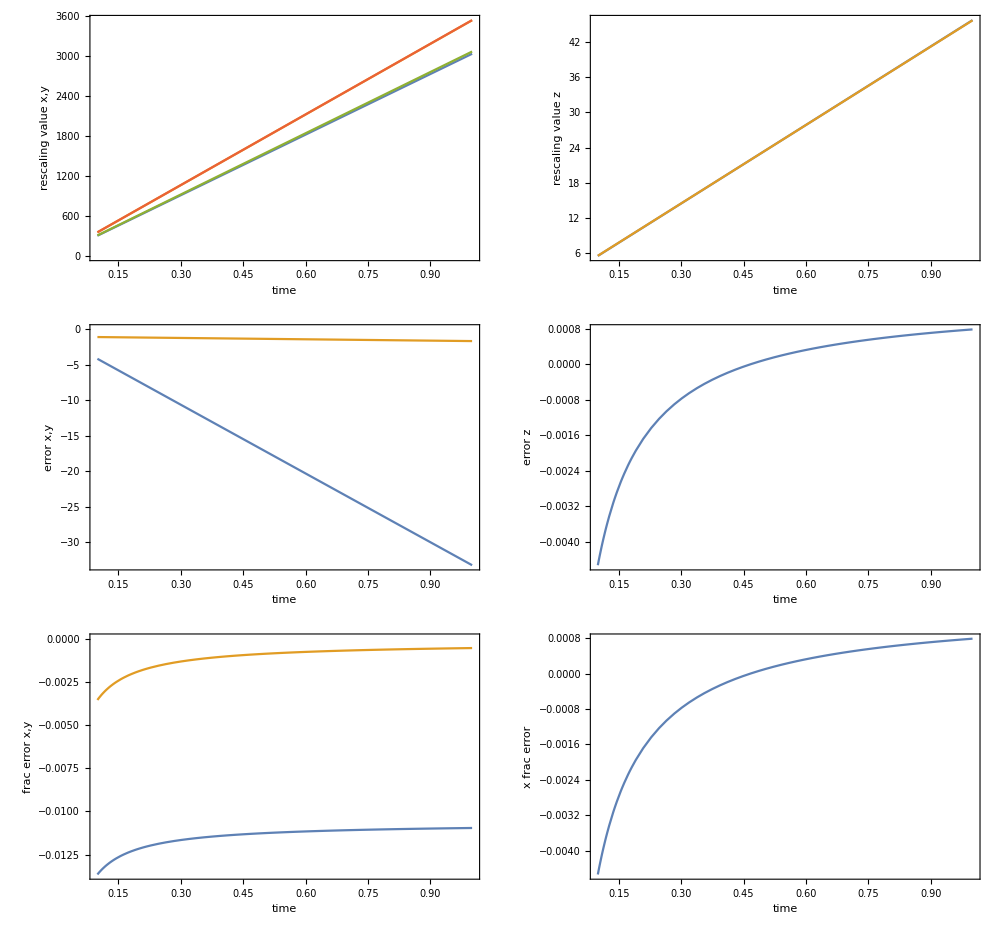

```mathematica
approxCigarHackExtendedAsmpAproxSoln={λx->1+(√2 t ωx √(ωx (ωx+ωy)))/(ωx+ωy),λy->1+(√2 t ωy √(ωy (ωx+ωy)))/(ωx+ωy),λz->1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2}
tmaxplot={0.1,1};
omegasamp={500,550,50}*2π;
makeComparisonPlots[tmaxplot,omegasamp,parametricScaling,approxCigarHackExtendedAsmpAproxSoln]
```

```mathematica
N[ReturnFracErr[0.1,{20,30,10},parametricScaling,approxCigarHackExtendedAsmpAproxSoln]]
```

{-0.32677,-0.483538,-0.158502}

```mathematica
N[ReturnFracErr[0.1,omegasamp,parametricScaling,approxCigarHackExtendedAsmpSoln]]
```

{-0.0136522,-0.00354884,-0.00453448}

## Direct solve attempts

```mathematica
AsyScaling=AsymptoticDSolveValue[{λx''[t]==(ωx)^2/((λx[t]^2)λy [t]λz[t]),λx'[0]==0,λx[0]==1,
λy''[t]==(ωy)^2/(λx[t](λy[t])^2 λz[t]),λy'[0]==0,λy[0]==1,
λz''[t]==(ωz)^2/(λx[t]λy[t] (λz[t])^2),λz'[0]==0,λz[0]==1},
{λx,λy,λz},{t,0,10},Assumptions->{ωx∈Reals,ωx>0,ωy∈Reals,ωy>0,ωz∈Reals,ωz>0,λx∈Reals,λy∈Reals,λz∈Reals}]
```

{1+(t^2 ωx^2)/2+1/24 t^4 (-2 ωx^4-ωx^2 ωy^2-ωx^2 ωz^2)+1/720 t^6 ωx^2 (22 ωx^4+15 ωx^2 ωy^2+8 ωy^4+15 ωx^2 ωz^2+8 ωy^2 ωz^2+8 ωz^4)-(t^8 ωx^2 (584 ωx^6+488 ωx^4 ωy^2+331 ωx^2 ωy^4+172 ωy^6+488 ωx^4 ωz^2+362 ωx^2 ωy^2 ωz^2+188 ωy^4 ωz^2+331 ωx^2 ωz^4+188 ωy^2 ωz^4+172 ωz^6))/40320+(t^10 ωx^2 (28384 ωx^8+27888 ωx^6 ωy^2+21405 ωx^4 ωy^4+14412 ωx^2 ωy^6+7136 ωy^8+27888 ωx^6 ωz^2+25278 ωx^4 ωy^2 ωz^2+17292 ωx^2 ωy^4 ωz^2+8640 ωy^6 ωz^2+21405 ωx^4 ωz^4+17292 ωx^2 ωy^2 ωz^4+8768 ωy^4 ωz^4+14412 ωx^2 ωz^6+8640 ωy^2 ωz^6+7136 ωz^8))/3628800,1+(t^2 ωy^2)/2+1/24 t^4 (-ωx^2 ωy^2-2 ωy^4-ωy^2 ωz^2)+1/720 t^6 ωy^2 (8 ωx^4+15 ωx^2 ωy^2+22 ωy^4+8 ωx^2 ωz^2+15 ωy^2 ωz^2+8 ωz^4)-(t^8 ωy^2 (172 ωx^6+331 ωx^4 ωy^2+488 ωx^2 ωy^4+584 ωy^6+188 ωx^4 ωz^2+362 ωx^2 ωy^2 ωz^2+488 ωy^4 ωz^2+188 ωx^2 ωz^4+331 ωy^2 ωz^4+172 ωz^6))/40320+(t^10 ωy^2 (7136 ωx^8+14412 ωx^6 ωy^2+21405 ωx^4 ωy^4+27888 ωx^2 ωy^6+28384 ωy^8+8640 ωx^6 ωz^2+17292 ωx^4 ωy^2 ωz^2+25278 ωx^2 ωy^4 ωz^2+27888 ωy^6 ωz^2+8768 ωx^4 ωz^4+17292 ωx^2 ωy^2 ωz^4+21405 ωy^4 ωz^4+8640 ωx^2 ωz^6+14412 ωy^2 ωz^6+7136 ωz^8))/3628800,1+(t^2 ωz^2)/2+1/24 t^4 (-ωx^2 ωz^2-ωy^2 ωz^2-2 ωz^4)+1/720 t^6 ωz^2 (8 ωx^4+8 ωx^2 ωy^2+8 ωy^4+15 ωx^2 ωz^2+15 ωy^2 ωz^2+22 ωz^4)-(t^8 ωz^2 (172 ωx^6+188 ωx^4 ωy^2+188 ωx^2 ωy^4+172 ωy^6+331 ωx^4 ωz^2+362 ωx^2 ωy^2 ωz^2+331 ωy^4 ωz^2+488 ωx^2 ωz^4+488 ωy^2 ωz^4+584 ωz^6))/40320+(t^10 ωz^2 (7136 ωx^8+8640 ωx^6 ωy^2+8768 ωx^4 ωy^4+8640 ωx^2 ωy^6+7136 ωy^8+14412 ωx^6 ωz^2+17292 ωx^4 ωy^2 ωz^2+17292 ωx^2 ωy^4 ωz^2+14412 ωy^6 ωz^2+21405 ωx^4 ωz^4+25278 ωx^2 ωy^2 ωz^4+21405 ωy^4 ωz^4+27888 ωx^2 ωz^6+27888 ωy^2 ωz^6+28384 ωz^8))/3628800}

Investigate error

{100 π,200 π,1000 π}

1/1000

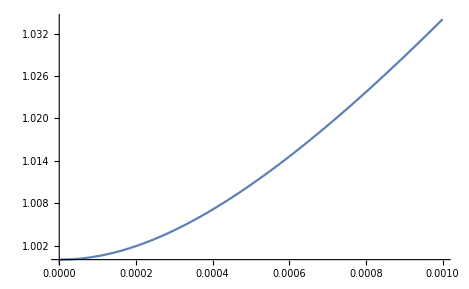

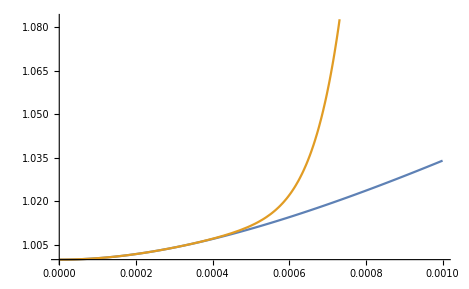

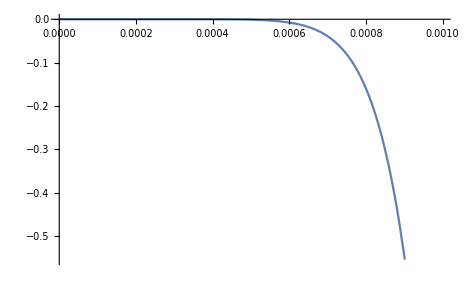

```mathematica
omegasamp={50,100,500}*2π
tmax=1 10^-3
Plot[(λx[Sequence@@omegasamp][t]/.parametricScaling),{t,0,tmax}]
Plot[{(λx[Sequence@@omegasamp][t]/.parametricScaling),(AsyScaling[[1]]/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})},{t,0,tmax}]
Plot[{(λx[Sequence@@omegasamp][t]/.parametricScaling)-(AsyScaling[[1]]/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})},{t,0,tmax}]
```

### Integration of parametric solution

```mathematica
Integrate[ωx^2/(AsyScaling[[1]]^2*AsyScaling[[2]]*AsyScaling[[3]]),t]
```

1/2 ωx^2 ((√2 ωx^3 (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2)+2 ((√2 ωy^5 ArcTan[(t ωy)/(√2)])/((ωx^2-ωy^2)^2 (ωy^2-ωz^2))+((t ωx^4 (ωx^2-ωz^2))/((2+t^2 ωx^2) (ωx^2-ωy^2))+(√2 ωz^5 ArcTan[(t ωz)/(√2)])/(-ωy^2+ωz^2))/((ωx^2-ωz^2)^2)))

```mathematica
scalingNestedIntegeration=1+t{Integrate[ωx^2/(AsyScaling[[1]]^2*AsyScaling[[2]]*AsyScaling[[3]]),t],Integrate[ωy^2/(AsyScaling[[2]]^2*AsyScaling[[1]]*AsyScaling[[3]]),t],Integrate[ωz^2/(AsyScaling[[3]]^2*AsyScaling[[1]]*AsyScaling[[2]]),t]}
```

{1+1/2 t ωx^2 ((√2 ωx^3 (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2)+2 ((√2 ωy^5 ArcTan[(t ωy)/(√2)])/((ωx^2-ωy^2)^2 (ωy^2-ωz^2))+((t ωx^4 (ωx^2-ωz^2))/((2+t^2 ωx^2) (ωx^2-ωy^2))+(√2 ωz^5 ArcTan[(t ωz)/(√2)])/(-ωy^2+ωz^2))/((ωx^2-ωz^2)^2))),1+1/2 t ωy^2 ((2 √2 ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2))+((√2 ωy^3 (ωy^4-3 ωy^2 ωz^2+ωx^2 (-3 ωy^2+5 ωz^2)) ArcTan[(t ωy)/(√2)])/((ωx^2-ωy^2)^2)+2 ((t ωy^4 (-ωy^2+ωz^2))/((ωx^2-ωy^2) (2+t^2 ωy^2))+(√2 ωz^5 ArcTan[(t ωz)/(√2)])/(-ωx^2+ωz^2)))/((ωy^2-ωz^2)^2)),1+1/2 t ωz^2 ((2 √2 ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2) (ωx^2-ωz^2)^2)+((2 √2 ωy^5 ArcTan[(t ωy)/(√2)])/(-ωx^2+ωy^2)+(ωz^3 (2 t ωz (-ωx^2+ωz^2) (-ωy^2+ωz^2)+√2 (2+t^2 ωz^2) (-3 ωy^2 ωz^2+ωz^4+ωx^2 (5 ωy^2-3 ωz^2)) ArcTan[(t ωz)/(√2)]))/((ωx^2-ωz^2)^2 (2+t^2 ωz^2)))/((ωy^2-ωz^2)^2))}

```mathematica
FullSimplify[scalingNestedIntegeration,Assumptions->{ωx∈Reals,ωx>0,ωy∈Reals,ωy>0,ωz∈Reals,ωz>0,λx∈Reals,λy∈Reals,λz∈Reals}]
```

{1+(t^2 ωx^6)/((2+t^2 ωx^2) (ωx^2-ωy^2) (ωx^2-ωz^2))+(t ωx^2 (ωx^3 (ωy-ωz) (ωy+ωz) (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) ArcTan[(t ωx)/(√2)]+2 ωy^5 (ωx^2-ωz^2)^2 ArcTan[(t ωy)/(√2)]-2 (ωx^2-ωy^2)^2 ωz^5 ArcTan[(t ωz)/(√2)]))/(√2 (ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2 (ωy^2-ωz^2)),1+(t^2 ωy^6)/((-ωx^2+ωy^2) (2+t^2 ωy^2) (ωy^2-ωz^2))+(t ωy^2 (2 ωx^5 (ωy^2-ωz^2)^2 ArcTan[(t ωx)/(√2)]+ωy^3 (ωx-ωz) (ωx+ωz) (ωy^4-3 ωy^2 ωz^2+ωx^2 (-3 ωy^2+5 ωz^2)) ArcTan[(t ωy)/(√2)]-2 (ωx^2-ωy^2)^2 ωz^5 ArcTan[(t ωz)/(√2)]))/(√2 (ωx^2-ωy^2)^2 (ωx^2-ωz^2) (ωy^2-ωz^2)^2),1+1/2 t ωz^2 ((2 √2 ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2) (ωx^2-ωz^2)^2)+((2 √2 ωy^5 ArcTan[(t ωy)/(√2)])/(-ωx^2+ωy^2)+(ωz^3 ((2 t (ωx-ωz) (ωy-ωz) ωz (ωx+ωz) (ωy+ωz))/(2+t^2 ωz^2)+√2 (5 ωx^2 ωy^2-3 (ωx^2+ωy^2) ωz^2+ωz^4) ArcTan[(t ωz)/(√2)]))/((ωx-ωz)^2 (ωx+ωz)^2))/((ωy-ωz)^2 (ωy+ωz)^2))}

{10 π,200 π,1000 π}

1

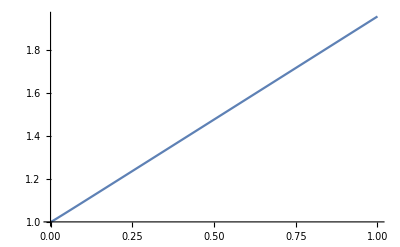

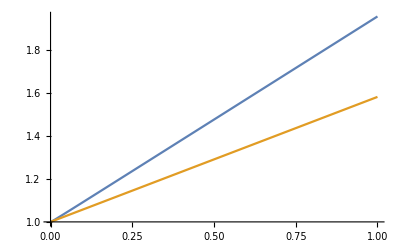

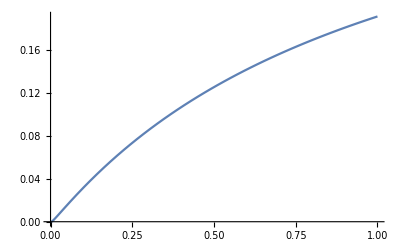

```mathematica
omegasamp={5,100,500}*2π
tmax=1 10^-0
Plot[(λx[Sequence@@omegasamp][t]/.parametricScaling),{t,0,tmax}]
Plot[{(λx[Sequence@@omegasamp][t]/.parametricScaling),(scalingNestedIntegeration[[1]]/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})},{t,0,tmax}]
Plot[{((λx[Sequence@@omegasamp][t]/.parametricScaling)-(scalingNestedIntegeration[[1]]/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]}))/(λx[Sequence@@omegasamp][t]/.parametricScaling)},{t,0,tmax}]
```

### Trial Integration

```mathematica
scalingNestedIntegeration=1+{0,0,0};
scalingNestedIntegeration=1+{Integrate[Integrate[ωx^2/(scalingNestedIntegeration[[1]]^2*scalingNestedIntegeration[[2]]*scalingNestedIntegeration[[3]]),t],t],Integrate[Integrate[ωy^2/(scalingNestedIntegeration[[2]]^2*scalingNestedIntegeration[[1]]*scalingNestedIntegeration[[3]]),t],t],Integrate[Integrate[ωz^2/(scalingNestedIntegeration[[3]]^2*scalingNestedIntegeration[[1]]*scalingNestedIntegeration[[2]]),t],t]}
scalingNestedIntegeration=1+{Integrate[Integrate[ωx^2/(scalingNestedIntegeration[[1]]^2*scalingNestedIntegeration[[2]]*scalingNestedIntegeration[[3]]),t],t],Integrate[Integrate[ωy^2/(scalingNestedIntegeration[[2]]^2*scalingNestedIntegeration[[1]]*scalingNestedIntegeration[[3]]),t],t],Integrate[Integrate[ωz^2/(scalingNestedIntegeration[[3]]^2*scalingNestedIntegeration[[1]]*scalingNestedIntegeration[[2]]),t],t]}
scalingNestedIntegeration=scalingNestedIntegeration
```

{1+(t^2 ωx^2)/2,1+(t^2 ωy^2)/2,1+(t^2 ωz^2)/2}

{1+(t ωx^5 (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) ArcTan[(t ωx)/(√2)])/(√2 (ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2)+(√2 t ωx^2 ωy^5 ArcTan[(t ωy)/(√2)])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2))+(√2 t ωx^2 ωz^5 ArcTan[(t ωz)/(√2)])/((-ωx^2+ωz^2)^2 (-ωy^2+ωz^2))-(ωx^4 Log[2+t^2 ωx^2])/(2 (-ωx^2+ωy^2) (ωx^2-ωz^2))-(ωx^4 (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) Log[2+t^2 ωx^2])/(2 (ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2)-(ωx^2 ωy^4 Log[2+t^2 ωy^2])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2))+(ωx^2 ωz^4 Log[2+t^2 ωz^2])/((ωx^2-ωz^2)^2 (ωy^2-ωz^2)),1+1/2 ωy^2 ((2 √2 t ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2))+(√2 t ωy^3 (-3 ωx^2 ωy^2+ωy^4+5 ωx^2 ωz^2-3 ωy^2 ωz^2) ArcTan[(t ωy)/(√2)])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2)^2)+(2 √2 t ωz^5 ArcTan[(t ωz)/(√2)])/((ωy^2-ωz^2)^2 (-ωx^2+ωz^2))-(2 ωx^4 Log[2+t^2 ωx^2])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2))+(2 (ωx^2 ωy^4-2 ωx^2 ωy^2 ωz^2+ωy^4 ωz^2) Log[2+t^2 ωy^2])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2)^2)+(2 ωz^4 Log[2+t^2 ωz^2])/((ωx^2-ωz^2) (ωy^2-ωz^2)^2)),1+1/2 ωz^2 ((2 √2 t ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2) (ωx^2-ωz^2)^2)+(2 √2 t ωy^5 ArcTan[(t ωy)/(√2)])/((-ωx^2+ωy^2) (ωy^2-ωz^2)^2)+(√2 t ωz^3 (5 ωx^2 ωy^2-3 ωx^2 ωz^2-3 ωy^2 ωz^2+ωz^4) ArcTan[(t ωz)/(√2)])/((ωy^2-ωz^2)^2 (-ωx^2+ωz^2)^2)-(2 ωx^4 Log[2+t^2 ωx^2])/((ωx^2-ωy^2) (ωx^2-ωz^2)^2)-(2 ωy^4 Log[2+t^2 ωy^2])/((-ωx^2+ωy^2) (ωy^2-ωz^2)^2)-(2 (2 ωx^2 ωy^2 ωz^2-ωx^2 ωz^4-ωy^2 ωz^4) Log[2+t^2 ωz^2])/((ωx^2-ωz^2)^2 (ωy^2-ωz^2)^2))}

{1+(t ωx^5 (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) ArcTan[(t ωx)/(√2)])/(√2 (ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2)+(√2 t ωx^2 ωy^5 ArcTan[(t ωy)/(√2)])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2))+(√2 t ωx^2 ωz^5 ArcTan[(t ωz)/(√2)])/((-ωx^2+ωz^2)^2 (-ωy^2+ωz^2))-(ωx^4 Log[2+t^2 ωx^2])/(2 (-ωx^2+ωy^2) (ωx^2-ωz^2))-(ωx^4 (ωx^4+5 ωy^2 ωz^2-3 ωx^2 (ωy^2+ωz^2)) Log[2+t^2 ωx^2])/(2 (ωx^2-ωy^2)^2 (ωx^2-ωz^2)^2)-(ωx^2 ωy^4 Log[2+t^2 ωy^2])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2))+(ωx^2 ωz^4 Log[2+t^2 ωz^2])/((ωx^2-ωz^2)^2 (ωy^2-ωz^2)),1+1/2 ωy^2 ((2 √2 t ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2))+(√2 t ωy^3 (-3 ωx^2 ωy^2+ωy^4+5 ωx^2 ωz^2-3 ωy^2 ωz^2) ArcTan[(t ωy)/(√2)])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2)^2)+(2 √2 t ωz^5 ArcTan[(t ωz)/(√2)])/((ωy^2-ωz^2)^2 (-ωx^2+ωz^2))-(2 ωx^4 Log[2+t^2 ωx^2])/((ωx^2-ωy^2)^2 (ωx^2-ωz^2))+(2 (ωx^2 ωy^4-2 ωx^2 ωy^2 ωz^2+ωy^4 ωz^2) Log[2+t^2 ωy^2])/((-ωx^2+ωy^2)^2 (ωy^2-ωz^2)^2)+(2 ωz^4 Log[2+t^2 ωz^2])/((ωx^2-ωz^2) (ωy^2-ωz^2)^2)),1+1/2 ωz^2 ((2 √2 t ωx^5 ArcTan[(t ωx)/(√2)])/((ωx^2-ωy^2) (ωx^2-ωz^2)^2)+(2 √2 t ωy^5 ArcTan[(t ωy)/(√2)])/((-ωx^2+ωy^2) (ωy^2-ωz^2)^2)+(√2 t ωz^3 (5 ωx^2 ωy^2-3 ωx^2 ωz^2-3 ωy^2 ωz^2+ωz^4) ArcTan[(t ωz)/(√2)])/((ωy^2-ωz^2)^2 (-ωx^2+ωz^2)^2)-(2 ωx^4 Log[2+t^2 ωx^2])/((ωx^2-ωy^2) (ωx^2-ωz^2)^2)-(2 ωy^4 Log[2+t^2 ωy^2])/((-ωx^2+ωy^2) (ωy^2-ωz^2)^2)-(2 (2 ωx^2 ωy^2 ωz^2-ωx^2 ωz^4-ωy^2 ωz^4) Log[2+t^2 ωz^2])/((ωx^2-ωz^2)^2 (ωy^2-ωz^2)^2))}

{20 π,200 π,1000 π}

1/10

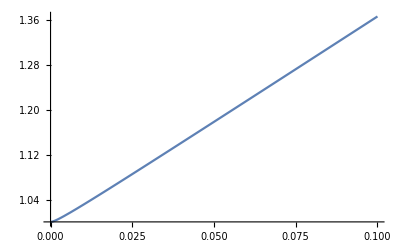

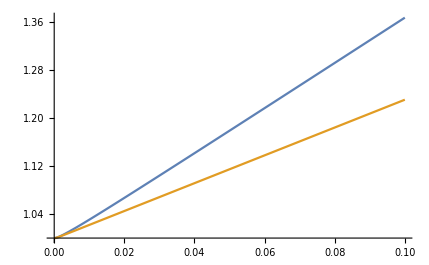

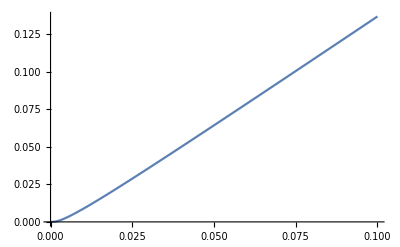

```mathematica
omegasamp={10,100,500}*2π
tmax=1 10^-1
Plot[(λx[Sequence@@omegasamp][t]/.parametricScaling),{t,0,tmax}]
Plot[{(λx[Sequence@@omegasamp][t]/.parametricScaling),(scalingNestedIntegeration[[1]]/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})},{t,0,tmax}]
Plot[{(λx[Sequence@@omegasamp][t]/.parametricScaling)-(scalingNestedIntegeration[[1]]/.{ωx->omegasamp[[1]],ωy->omegasamp[[2]],ωz->omegasamp[[3]]})},{t,0,tmax}]
```

### sph. symetric

```mathematica
assum={t∈Reals,λr∈Reals,ωr∈Reals,ωr>0}
```

{t∈ℝ,λr∈ℝ,ωr∈ℝ,ωr>0}

```mathematica
DSolve[{λr''[t]==(1)^2/(λr[t])^4,λr'[0]==0,λr[0]==1},
{λr},{t}]
```

{}

```mathematica
DSolve[{λr''[t]==(1)^2/(λr[t])^4,λr'[0]==0},
{λr},{t}]
```

{}

```mathematica
fx=1/x^4
D[fx,{x,n}]
SeriesExpansion=Sum[D[fx,{x,n}] x/(n!),{n,10}]
```

1/x^4

x^(-4-n) FactorialPower[-4,n]

286/x^13-220/x^12+165/x^11-120/x^10+84/x^9-56/x^8+35/x^7-20/x^6+10/x^5-4/x^4

```mathematica
(SeriesExpansion/.x->λr)
```

286/λr^13-220/λr^12+165/λr^11-120/λr^10+84/λr^9-56/λr^8+35/λr^7-20/λr^6+10/λr^5-4/λr^4

```mathematica
DSolve[{(λr''[t]==(SeriesExpansion/.x->λr)),λr'[0]==0,λr[0]==1},
{λr},{t}]
```

DSolve[{λr''[t]==286/λr^13-220/λr^12+165/λr^11-120/λr^10+84/λr^9-56/λr^8+35/λr^7-20/λr^6+10/λr^5-4/λr^4,λr'[0]==0,λr[0]==1},{λr},{t}]

```mathematica
NDSolve[{λr''[t]==(1)^2/(λr[t])^4,λr'[0]==0,λr[0]==1},
{λr},{t,0,2},AccuracyGoal->5]
```

{{λr→InterpolatingFunction[…]}}

```mathematica
DavidsSphSoln=(25/6 ωr^2)^(1/5)(t+0)^(2/5);
```

```mathematica
D[DavidsSphSoln,{t,2}]
ωr^2/DavidsSphSoln^4
```

-(6^(4/5) (ωr^2)^(1/5))/(5 5^(3/5) t^(8/5))

(6^(4/5) (ωr^2)^(1/5))/(5 5^(3/5) t^(8/5))

```mathematica
Solve[DavidsSphSoln==0,t]
```

{{t→0}}

```mathematica
Limit[D[DavidsSphSoln,{t,1}],t->0]
```

Indeterminate

{λr→ParametricFunction[<>]}

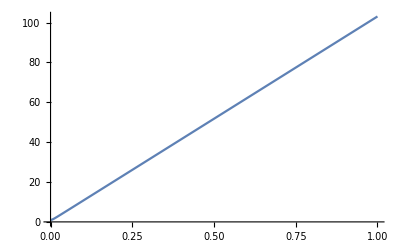

```mathematica
parametricScalingSphSym=ParametricNDSolve[{λr''[t]==(ωr)^2/(λr[t])^4,λr'[0]==0,λr[0]==1},
{λr},{t,0,2},{ωr},AccuracyGoal->5]
omegasamp=20*2π;
Plot[λr[omegasamp][t]/.parametricScalingSphSym,{t,0,1}]
```

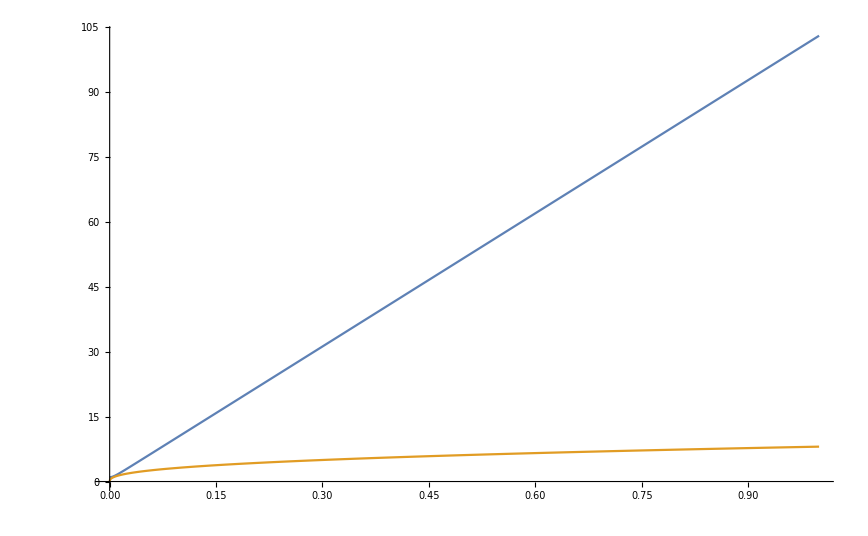

```mathematica
Plot[{λr[omegasamp][t]/.parametricScalingSphSym,
DavidsSphSoln/.{ωr->omegasamp}},{t,0,1}]
```

```mathematica
AsyScaling=AsymptoticDSolveValue[{λr''[t]==(ωr)^2/(λr[t])^4,λr'[0]==0,λr[0]==1},
{λr},{t,0,10}]
```

1+(t^2 ωr^2)/2-(t^4 ωr^4)/6+(19 t^6 ωr^6)/180-(59 t^8 ωr^8)/720+(4571 t^10 ωr^10)/64800

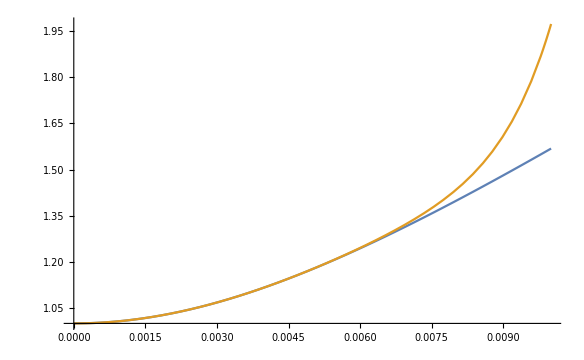

```mathematica
omegasamp=20*2π;
tmax=0.01;
Plot[{(λr[omegasamp][t]/.parametricScalingSphSym),(AsyScaling/.{ωr->omegasamp})},{t,0,tmax}]
```

```mathematica
scalingNestedIntegeration=1;
scalingNestedIntegeration=1+Integrate[Integrate[ωr^2/scalingNestedIntegeration^4,t],t]
scalingNestedIntegeration=1+scalingNestedIntegeration-(scalingNestedIntegeration/.t->0)
scalingNestedIntegeration=1+Integrate[Integrate[ωr^2/scalingNestedIntegeration^4,t],t]
scalingNestedIntegerationHack=20/17 scalingNestedIntegeration (*hack factor for long time agreement*)

scalingNestedIntegerationHack=1+scalingNestedIntegerationHack-(scalingNestedIntegerationHack/.t->0)

FullSimplify[scalingNestedIntegerationHack,Assumptions->assum]
```

1+(t^2 ωr^2)/2

1+(t^2 ωr^2)/2

1+1/48 ωr (-16/(ωr (2+t^2 ωr^2)^2)-20/(ωr (2+t^2 ωr^2))+15 √2 t ArcTan[(t ωr)/(√2)])

20/17 (1+1/48 ωr (-16/(ωr (2+t^2 ωr^2)^2)-20/(ωr (2+t^2 ωr^2))+15 √2 t ArcTan[(t ωr)/(√2)]))

1/6+20/17 (1+1/48 ωr (-16/(ωr (2+t^2 ωr^2)^2)-20/(ωr (2+t^2 ωr^2))+15 √2 t ArcTan[(t ωr)/(√2)]))

1/204 (274-80/((2+t^2 ωr^2)^2)-100/(2+t^2 ωr^2)+75 √2 t ωr ArcTan[(t ωr)/(√2)])

-0.00242426

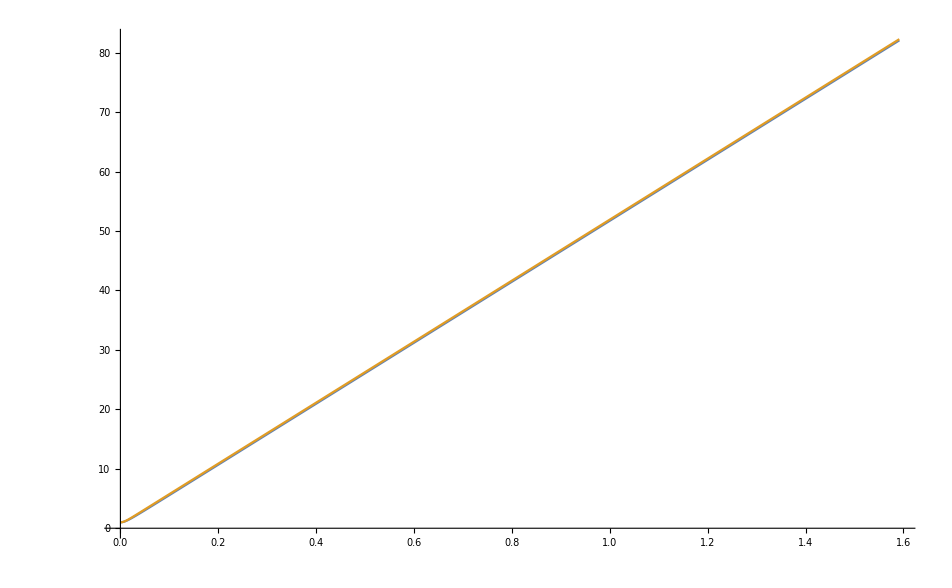

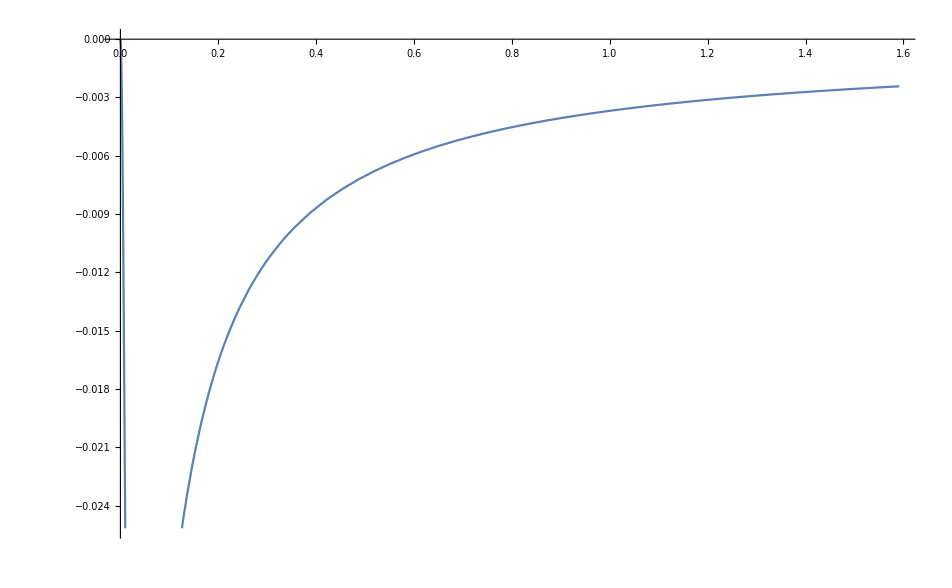

```mathematica
omegasamp=10*2π;
tmax=100/omegasamp;
diff=(((λr[omegasamp][t]/.parametricScalingSphSym)-(scalingNestedIntegerationHack/.{ωr->omegasamp}))/(λr[omegasamp][t]/.parametricScalingSphSym))/.t->tmax
Plot[{(λr[omegasamp][t]/.parametricScalingSphSym),(scalingNestedIntegerationHack/.{ωr->omegasamp})},{t,0,tmax}]
Plot[{(((λr[omegasamp][t]/.parametricScalingSphSym)-(scalingNestedIntegerationHack/.{ωr->omegasamp}))/(λr[omegasamp][t]/.parametricScalingSphSym))},{t,0,tmax}]
```

```mathematica
scalingNestedIntegerationHackAsmp=Simplify[1+t*Limit[D[scalingNestedIntegerationHack,t],t->∞],Assumptions->assum]
```

1+(25 π t ωr)/(68 √2)

-0.24127

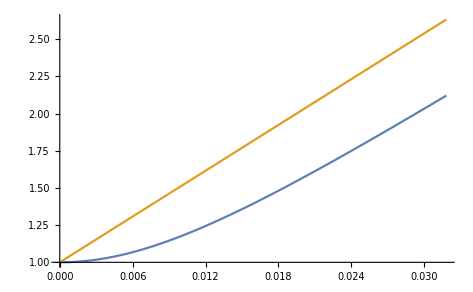

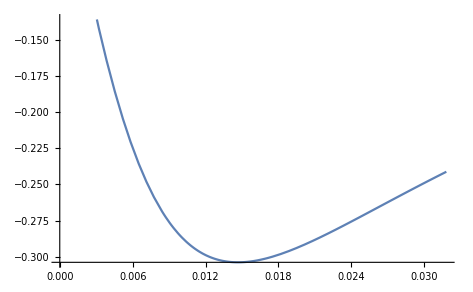

```mathematica
omegasamp=10*2π;
tmax=2/omegasamp;
diff=(((λr[omegasamp][t]/.parametricScalingSphSym)-(scalingNestedIntegerationHackAsmp/.{ωr->omegasamp}))/(λr[omegasamp][t]/.parametricScalingSphSym))/.t->tmax
Plot[{(λr[omegasamp][t]/.parametricScalingSphSym),(scalingNestedIntegerationHackAsmp/.{ωr->omegasamp})},{t,0,tmax}]
Plot[{(((λr[omegasamp][t]/.parametricScalingSphSym)-(scalingNestedIntegerationHackAsmp/.{ωr->omegasamp}))/(λr[omegasamp][t]/.parametricScalingSphSym))},{t,0,tmax}]
```

```mathematica
0.015*omegasamp
```

0.942478

```mathematica
|
```

```mathematica
|
```

```mathematica
scalingNestedIntegeration=1;
scalingNestedIntegeration=1+Integrate[Integrate[ωr^2/scalingNestedIntegeration^4,t],t]
scalingNestedIntegeration=1+scalingNestedIntegeration-(scalingNestedIntegeration/.t->0)
scalingNestedIntegeration=1+Integrate[Integrate[ωr^2/scalingNestedIntegeration^4,t],t]
scalingNestedIntegeration=1+scalingNestedIntegeration-(scalingNestedIntegeration/.t->0)
```

1+(t^2 ωr^2)/2

1+(t^2 ωr^2)/2

1+1/48 ωr (-16/(ωr (2+t^2 ωr^2)^2)-20/(ωr (2+t^2 ωr^2))+15 √2 t ArcTan[(t ωr)/(√2)])

31/24+1/48 ωr (-16/(ωr (2+t^2 ωr^2)^2)-20/(ωr (2+t^2 ωr^2))+15 √2 t ArcTan[(t ωr)/(√2)])

```mathematica
scalingNestedIntegeration=Integrate[ωr^2/scalingNestedIntegeration^4,t,Assumptions->assum]
scalingNestedIntegeration=t*(scalingNestedIntegeration-(scalingNestedIntegeration/.t->0))

FullSimplify[scalingNestedIntegeration,Assumptions->assum]
```

$Aborted

t^2 (7/24+1/48 ωr (-16/(ωr (2+t^2 ωr^2)^2)-20/(ωr (2+t^2 ωr^2))+15 √2 t ArcTan[(t ωr)/(√2)]))

1/48 t^3 ωr ((2 t ωr (18+7 t^2 ωr^2))/((2+t^2 ωr^2)^2)+15 √2 ArcTan[(t ωr)/(√2)])

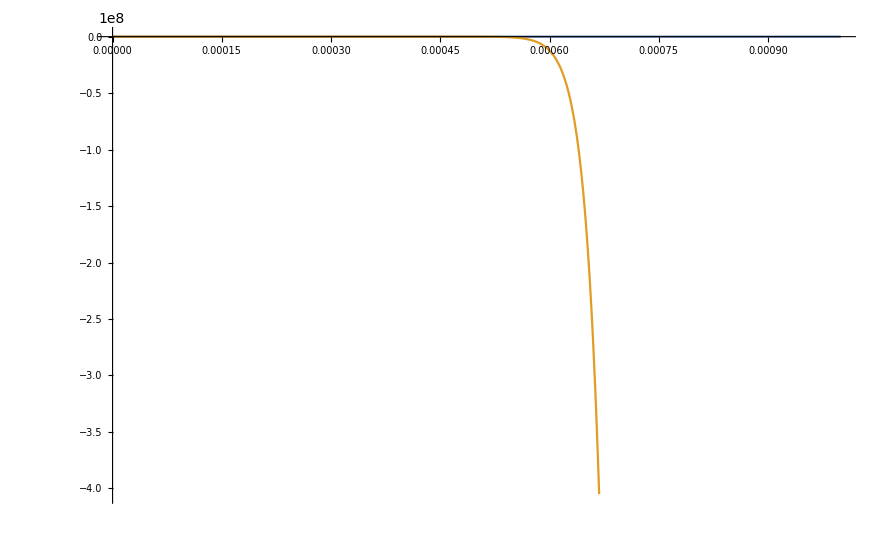

```mathematica
omegasamp=500*2π;
tmax=0.001;
Plot[{(λr[omegasamp][t]/.parametricScalingSphSym),(scalingNestedIntegeration/.{ωr->omegasamp})},{t,0,tmax}]
```

```mathematica
omegasamp=20*2π;
tmax=0.1;
Plot[{(λr[omegasamp][t]/.parametricScaling),(scalingNestedIntegeration/.{ωr->omegasamp})},{t,0,tmax}]
```

```mathematica
AsyScaling=DSolveValue[{λr''[t]==(ωr)^2/(λr[t])^4,λr'[0]==0,λr[0]==1},
{λr},{t,0,2},Assumptions->{ωr∈Reals,ωr>0,λr∈Reals}]
```

DSolveValue::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

DSolveValue[{λr''[t]==ωr^2/λr[t]^4,λr'[0]==0,λr[0]==1},{λr},{t,0,2},Assumptions→{ωr∈ℝ,ωr>0,λr∈ℝ}]